## Intro Mathematica

```mathematica
1+1; (*semicolon: no execution *)
```

Execute : Shift + Enter or Enter on far right

```mathematica
f[x_]:= Sin[x^2-Cos[x]]+x^2//N; (*note cap in Sin *) 
g[x_]:=3x;(*//N : forces numerical *)
f[2]
```

3.04356

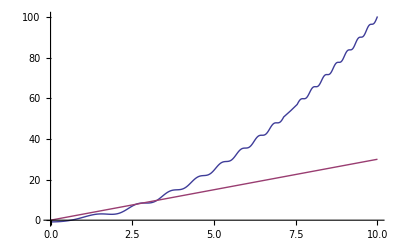

```mathematica
Plot[{f[x],g[x]},{x,0,10}] (*needs range *)
```

## Tables

```mathematica
tt={2,3,2,6};
```

```mathematica
{2,3,2,6};
ss=Table[i^2,{i,1,10}];

cc=Table[{i,j,4},{i,1,3},{j,3,4}];
MatrixForm[cc]
```

((1
3
4) | (1
4
4)
(2
3
4) | (2
4
4)
(3
3
4) | (3
4
4))

## Plotting :

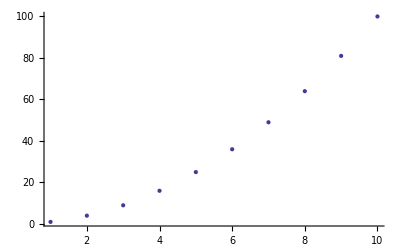

```mathematica
ListPlot[ss]
```

## Curves

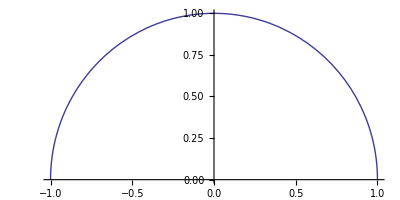

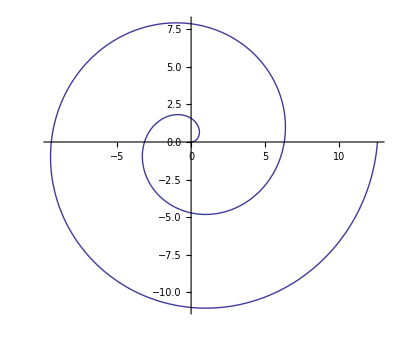

```mathematica
curve[t_]:={Cos[t],Sin[t]}; (*parametric curve: circle *)
ParametricPlot[curve[t],{t,0,Pi}]

curve2[t_]:={t*Cos[t],t*Sin[t]};
ParametricPlot[curve2[t],{t,0,4Pi}]
```

```mathematica
f3[t_]:={t,t^2,t^3};
ParametricPlot3D[f3[t],{t,0,1},Boxed-> False]
```

-Graphics3D-

```mathematica
surf[u_,v_]:={u,v,u^2*Sin[v^2]};
ParametricPlot3D[surf[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-